## ECE 533 HW#1A - Devin Bresser

#### Problem 1(a)

```mathematica
rr = RandomReal[1, {20,30}];
```

#### Problem 1(b)

```mathematica
MatrixForm[rr];
```

This method of displaying the data takes the 20 x 30 2-dimensional array generated by RandomReal and converts it to a traditional matrix with the dimensions 20 x 30. It then displays the matrix.

#### Problem 1(c)

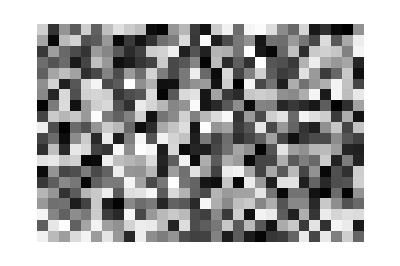

```mathematica
ArrayPlot[rr]
```

This method of displaying the data has converted the 20x30 array into an image with 20 x 30 pixel dimensions.
Each pixel of the image is a grayscale pixel, a real number between 0 and 1, where 0 is fully white and 1 is fully black.

#### Problem 1(d)

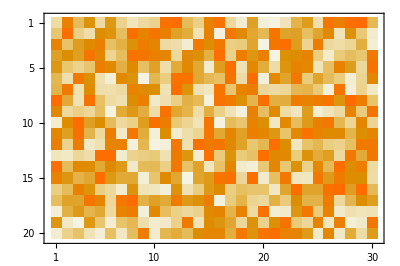

```mathematica
MatrixPlot[rr]
```

This method of displaying the data has converted the 20x30 array into an image again like the previous function.
This time, the appearance of each pixel has a color instead of grayscale. It seems like the default option for this is that 1 is orange and 0 is still white.

#### Problem 1(e)

```mathematica
Image[rr]
```

-Graphics-

This method of displaying the data has displayed the matrix as an array of pixels just as ArrayPlot did. 
However, this time, the image is scaled relative to the screen. Thus the 20 x 30 pixel image appears very small compared to the screen which has a resolution of 2888 x 1864 pixels.

#### Problem 1(f)

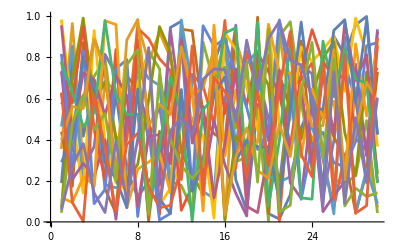

```mathematica
ListPlot[rr, Joined->True]
```

This method of displaying the data has plotted all 20 of the 30-point lists all on top of each other.
The x-index of each plot is simply the index of that point within the list.
Adding the Joined -> True option chains the points together forming a line.

#### Problem 1(g)

```mathematica
ListPlot3D[rr]
```

-Graphics3D-

This method of displaying the data is just the same as ListPlot but the plot is now displayed in 3D.
That is, each curve from ListPlot is displayed as before, but a third dimension “behind” each curve has been added to the plot. I think of it like a crumpled pieces of paper, looking at them head on versus at an angle.

#### Problem 1(h)

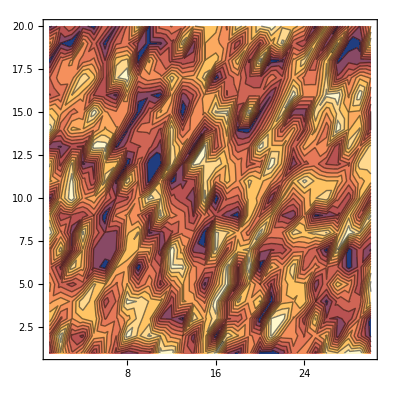

```mathematica
ListContourPlot[rr]
```

This function provides a “top down” view of the ListPlot3D and uses contour lines and shading to represent the “high” and “low” parts of each line.

#### Problem 2(a)

```mathematica
a = {1,2,x,y}
b = {5,z,4,3};
Dimensions[a]
```

{1,2,x,y}

{4}

```mathematica
{a+b, a*b, a.b, Sin[a+b]}
```

{{6,2+z,4+x,3+y},{5,2 z,4 x,3 y},5+4 x+3 y+2 z,{Sin[6],Sin[2+z],Sin[4+x],Sin[3+y]}}

#### Problem 2(b)

```mathematica
m= {a,b};
Dimensions[m]
MatrixForm[m]
```

{2,4}

(1 | 2 | x | y
5 | z | 4 | 3)

#### Problem 2(c)

```mathematica
ma = m.a
Dimensions[ma]
```

{5+x^2+y^2,5+4 x+3 y+2 z}

{2}

#### Problem 2(d)

```mathematica
mb = m.b
```

{5+4 x+3 y+2 z,50+z^2}

```mathematica
mamb = Flatten[{ma, mb}]
```

{5+x^2+y^2,5+4 x+3 y+2 z,5+4 x+3 y+2 z,50+z^2}

```mathematica
Dimensions[mamb]
```

{4}

#### Problem 2(d) (2)

```mathematica
m34 = {Part[m,1], Part[m,2], mamb}
MatrixForm[m34]
```

{{1,2,x,y},{5,z,4,3},{5+x^2+y^2,5+4 x+3 y+2 z,5+4 x+3 y+2 z,50+z^2}}

(1 | 2 | x | y
5 | z | 4 | 3
5+x^2+y^2 | 5+4 x+3 y+2 z | 5+4 x+3 y+2 z | 50+z^2)

#### Problem 2(e)

```mathematica
mParte = {Part[m34,1],Part[m34,2],Part[m34,3],{1,2,3,4}}
MatrixForm[mParte]
Dimensions[mParte]
```

{{1,2,x,y},{5,z,4,3},{5+x^2+y^2,5+4 x+3 y+2 z,5+4 x+3 y+2 z,50+z^2},{1,2,3,4}}

(1 | 2 | x | y
5 | z | 4 | 3
5+x^2+y^2 | 5+4 x+3 y+2 z | 5+4 x+3 y+2 z | 50+z^2
1 | 2 | 3 | 4)

{4,4}

#### Problem 2(f)

```mathematica
Det[mParte]
```

1335-573 x+82 x^2+6 x^3-186 y+47 x y-8 x^2 y+11 y^2+6 x y^2-8 y^3-224 z+80 x z-4 x^3 z+20 y z-4 x y z+3 x^2 y z-3 y^2 z-4 x y^2 z+3 y^3 z+38 z^2-10 x z^2-2 y z^2-3 z^3+x z^3

#### Problem 2(g)

```mathematica
middlefour= {mParte[[2,2]], mParte[[2,3]], mParte[[3,2]], mParte[[3,3]]}
```

{z,4,5+4 x+3 y+2 z,5+4 x+3 y+2 z}

#### Problem 3(a)

```mathematica
mproblem3 = RandomReal[1, {20,30}];
```

#### Problem 3(b)

```mathematica
iR = Image[mproblem3, ImageSize ->100]
```

-Graphics-

```mathematica
iR = Image[mproblem3, ImageSize ->300]
```

-Graphics-

```mathematica
iR= Image[mproblem3, ImageSize ->800]
```

-Graphics-

#### Problem 3(c)

```mathematica
Export["iR.tif",iR ]
```

iR.tif

#### Problem 3(d)

```mathematica
importediRtif= Import["/Users/devin/iR.tif"]
```

-Graphics-

#### Problem 3(e)

```mathematica
ImageDimensions [iR]
ImageDimensions[importediRtif]
```

{30,20}

{30,20}

Dimensions agree.

#### Problem 3(f)

```mathematica
Dimensions[ImageData[iR]]
Dimensions[ImageData[importediRtif]]
```

{20,30}

{20,30}

```mathematica
Max[Abs[ Dimensions[ImageData[iR]]-Dimensions[ImageData[importediRtif]]]]
```

0

For tif file format, dimensions agree and difference is 0.

#### Problem 3(g) (.gif file format)

```mathematica
Export["iR.gif",iR ]
importediRgif = Import["/Users/devin/iR.gif"]
```

iR.gif

-Graphics-

```mathematica
ImageDimensions [importediRtif]
ImageDimensions[importediRgif]
```

{30,20}

{30,20}

```mathematica
Dimensions[ImageData[importediRtif]]
Dimensions[ImageData[importediRgif]]
FileSize["/Users/devin/iR.tif"]
FileSize["/Users/devin/iR.gif"]
```

{20,30}

{20,30,3}

1.628 kB

1.542 kB

The .gif file format has an additional dimension, with a value of 3.
I assume this to mean that the .gif file format has R,G,B values in the matrix as well.
The .gif format is also slightly smaller in terms of file size.

#### Problem 3(h) (.jpg file format)

```mathematica
Export["iR.jpg",iR ]
importediRjpg = Import["/Users/devin/iR.jpg"]
```

iR.jpg

-Graphics-

```mathematica
ImageDimensions [iR]
ImageDimensions[importediRjpg]
```

{30,20}

{30,20}

```mathematica
Dimensions[ImageData[iR]]
Dimensions[ImageData[importediRjpg]]
FileSize["/Users/devin/iR.tif"]
FileSize["/Users/devin/iR.jpg"]
```

{20,30}

{20,30}

1.628 kB

0.959 kB

The ImageDimensions and the dimensions of the ImageData are identical for .tif vs .jpg
However, the .jpg file format is substantially smaller than the .tif file format. 
This means that some sort of compression has been done on the image.